```mathematica
img=-Graphics-
img = Binarize[img~ColorConvert~"Grayscale"~ImageResize~500~Blur~3];
pts = DeleteDuplicates@
   Cases[Normal@
      ListContourPlot[Reverse@ImageData[img], 
       Contours -> {0.5}], _Line, -1][[1, 1]];
center = Mean@MinMax[pts] & /@ Transpose@pts;
pts = # - center & /@ pts[[;; ;; 20]];
EpicyclePlot = ListPlot[pts, AspectRatio -> Automatic]
```

-Graphics-

The points here are mapped from the image above, which form a closed curve. We can transform each points into complex numbers (z) and take the discrete Fourier Transform (c.n[ ]) up to a prescribed order (m). This provides a parametric curve that follows the integral before as:

we can change the amount of epicycles present by using changing the m value. The amount of epicycle orbits present or shown within the animation is  (not including the initial orbit).

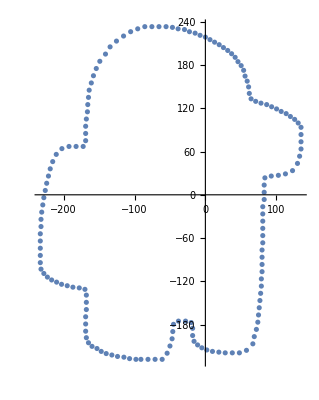

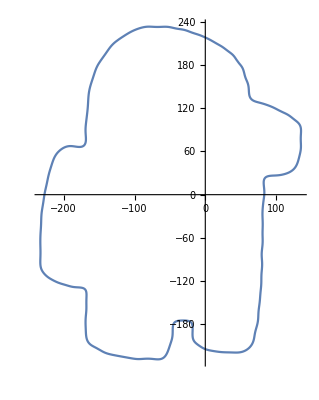

```mathematica
SetAttributes[toPt,Listable]
toPt[z_]:=ComplexExpand[{Re@z,Im@z}]//Chop;
cf=Compile[{{z,_Complex,1}},Module[{n=Length@z},1/n*Table[Sum[z[[k]]*Exp[-I*i*k*2 Pi/n],{k,1,n}],{i,-m,m}]]];
z=pts[[All,1]]+I*pts[[All,2]];
m=60;
cn=cf[z];
{f[t_],g[t_]}=Sum[cn[[j]]*Exp[I*(j-m-1)*t],{j,1,2 m+1}]//toPt;
ParametricPlot[{f[t],g[t]},{t,0,2 Pi},AspectRatio->Automatic]
```

```mathematica
r = Abs /@ cn;
theta = Arg /@ cn;
index = {m + 1}~Join~
   Riffle[Range[m + 2, 2 m + 1], Reverse[Range[1, m]]];
p[t_] = Accumulate@Table[cn[[j]]*Exp[I*(j - m - 1)*t], {j, index}] // toPt;
circles[t_] = 
  Table[Circle[p[t][[i-1]], r[[index[[i]]]]], {i, 2, 2 m + 1}];

anims = ParallelTable[
   ParametricPlot[{f[s], g[s]}, {s, 0, t}, AspectRatio -> Automatic,
     Epilog -> {circles[t], Line[p[t]], Point[p[t]]}, 
     PlotRange -> {{-400, 400}, {-400, 400}}, 
     ImageSize -> 500],
   {t, Subdivide[0.1, 4 Pi, 100]}];
gif=ListAnimate@anims
```

```mathematica
Export["Amog us.gif",Flatten[{anims,Table[anims[[i]],{i,Length[anims]-1,2,-1}]}]]
```

Amog us.gif

```mathematica
SystemOpen["Amog us.gif"]
```